```mathematica
MatrixForm[A = {{0,0},{1,8},{3,8},{4,20}}]
```

(0 | 0
1 | 8
3 | 8
4 | 20)

```mathematica
MatrixForm[standardA=Standardize[A,Mean,1&]]
```

(-2 | -9
-1 | -1
1 | -1
2 | 11)

```mathematica
Transpose[standardA].standardA
```

{{10,40},{40,204}}

```mathematica
Eigensystem[Transpose[standardA].standardA]
```

{{107+√11009,107-√11009},{{1/40 (-97+√11009),1},{1/40 (-97-√11009),1}}}

```mathematica
N[107-√11009]
```

2.07622

```mathematica
a=40;
b=90-Sqrt[11009];
c=-953+9 Sqrt[11009];
f[x_]:=(40 x)/(-97+Sqrt[11009])+9-80/(-97+Sqrt[11009]);
```

```mathematica
MatrixForm[N[Table[{Abs[a A⟦i,1⟧+b A⟦i,2⟧+c]/Sqrt[a^2+b^2],Abs[A⟦i,2⟧-f[A⟦i,1⟧]]},{i,4}]]]
```

(0.20345 | 1.09619
2.063 | 4.04809
0.189168 | 6.04809
3.44695 | 0.903811)

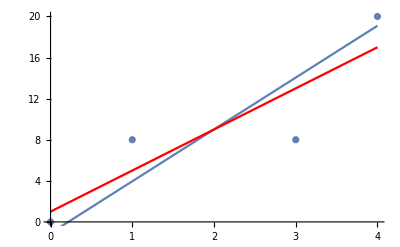

```mathematica
Show[ListPlot[Table[A⟦i⟧,{i,4}]],Plot[f[x],{x,0,4}],Plot[1+4 x,{x,0,4},PlotStyle->Red]]
```

```mathematica
circledata={{-4,3},{-3,1},{-3,3},{-1,-1},{-1,2}};
triangledata={{1,1},{3,-4},{3,-2},{4,-3}};
circleConstraints=Apply[And,Table[{w1,w2}.x+b≥1,{x,circledata}]];
triangleConstraints=Apply[And,Table[{w1,w2}.x+b≤-1,{x,triangledata}]];
allConstraints=Join[circleConstraints,triangleConstraints];
X=Join[circledata,-triangledata];
Y=Join[ConstantArray[1,Length[circledata]],ConstantArray[-1,Length[triangledata]]]
e=ConstantArray[1,Length[X]]
λ=Table[λi[i],{i,Length[X]}]
NMaximize[{-0.5 λ.X.Transpose[X].λ+λ.e,λ>0,λ.Y==0},λ]
```

{1,1,1,1,1,-1,-1,-1,-1}

{1,1,1,1,1,1,1,1,1}

{λi[1],λi[2],λi[3],λi[4],λi[5],λi[6],λi[7],λi[8],λi[9]}

{0.5,{λi[1]→0.,λi[2]→2.14841×10^-29,λi[3]→-1.89327×10^-29,λi[4]→0.166667,λi[5]→0.333333,λi[6]→0.5,λi[7]→1.0626×10^-27,λi[8]→0.,λi[9]→-3.00137×10^-30}}

```mathematica
A={{-4,3},{-3,3},{-1,2},{3,-2},{3,-4},{4,-3}};
circledata=A⟦1;;3⟧;
triangledata=A⟦4;;6⟧;
circleConstraints=Apply[And,Table[{w1,w2}.x+b≥1,{x,circledata}]];
triangleConstraints=Apply[And,Table[{w1,w2}.x+b≤-1,{x,triangledata}]];
allConstraints=Join[circleConstraints,triangleConstraints];
X=Join[circledata,-triangledata];
Y=Join[ConstantArray[1,Length[circledata]],ConstantArray[-1,Length[triangledata]]]
e=ConstantArray[1,Length[X]]
λ=Table[λi[i],{i,Length[X]}]
NMaximize[{-0.5 λ.X.Transpose[X].λ+λ.e,λ>0,λ.Y==0},λ]
```

{1,1,1,-1,-1,-1}

{1,1,1,1,1,1}

{λi[1],λi[2],λi[3],λi[4],λi[5],λi[6]}

{0.0625,{λi[1]→3.26638×10^-30,λi[2]→-1.08666×10^-28,λi[3]→0.0625,λi[4]→0.0625,λi[5]→2.72404×10^-30,λi[6]→5.42342×10^-31}}

```mathematica
Solve[{-x-y+z==-1,-x+2 y+z==0,x+y-z==0},{x,y,z}]
```

{}